# Data consolidation

This notebook is for analyzing data produced by analysis_guppy, analysis_ILM, and analysis_k.

## Initialization

#### Initialize functions

```mathematica
SetDirectory[NotebookDirectory[]];
<<Functions_master.wl;
```

Create a new spreadsheet: run this if you changed something in the individual sample folders and need to re-compile

```mathematica
compileStatswithILM;
```

```mathematica
d1 =  FileDate[NotebookFileName[], "Modification"];
d2 = FileDate["Functions_master.wl", "Modification"];
Style["Last updated by Leanne Friedrich on "<>DateString[Max[{d1,d2}], {"MonthName", " ", "DayShort", ", ", "Year", " at ", "Hour12Short",":","Minute"," ", "AMPMLowerCase"}],{"Text", Large}]
```

Last updated by Leanne Friedrich on April 25, 2017 at 8:46 pm

## Interfaces

### Find stats for individual samples

```mathematica
FindProfiles
```

```mathematica
findDirectoriesInterface
```

### Plot

```mathematica
plotInterface
```

```mathematica
1/1.08
```

0.925926

### Covariance

```mathematica
covInterface
```

## old stuff

### ANOVA

```mathematica
anovaInterface
```

### Contours

```mathematica
getContours[14]
```

### Colors

```mathematica
Row[{Grid@Transpose[Prepend[Prepend[Transpose[Table[ColorData[i][j],{i, ColorData["Gradients"]},{j, (Range[0,3]/3)}]], ColorData["Gradients"]], Range[1,51]] ], "     ", Grid@Table[ColorData[i][j],{i, ColorData["Gradients"]},{j, (Range[0,2]/2)}]}]
```

1 | AlpineColors | RGBColor[0.277546, 0.355398, 0.484215] | RGBColor[0.3769963333333333, 0.49729866666666667, 0.36058866666666667] | RGBColor[0.651902, 0.6609073333333333, 0.5771666666666666] | RGBColor[1., 0.997467, 0.914244]
2 | Aquamarine | RGBColor[0.68069, 0.735561, 0.850004] | RGBColor[0.7099796666666667, 0.7875856666666666, 0.8332186666666667] | RGBColor[0.5106996666666667, 0.6759666666666666, 0.737415] | RGBColor[0.631571, 0.734035, 0.848615]
3 | ArmyColors | RGBColor[0.45684, 0.59295, 0.506035] | RGBColor[0.529818, 0.5929986666666667, 0.425935] | RGBColor[0.608209, 0.5623436666666667, 0.44886966666666667] | RGBColor[0.762737, 0.757717, 0.654841]
4 | AtlanticColors | RGBColor[0.131838, 0.159976, 0.163333] | RGBColor[0.423197, 0.5634193333333334, 0.5820403333333333] | RGBColor[0.551935, 0.720859, 0.807507] | RGBColor[0.479438, 0.4981, 0.622843]
5 | AuroraColors | RGBColor[0.258824, 0.258824, 0.258824] | RGBColor[0.4232666666666667, 0.314267, 0.35999933333333334] | RGBColor[0.5786533333333334, 0.6371166666666667, 0.5929513333333334] | RGBColor[0.8619, 0.275798, 0.951756]
6 | AvocadoColors | RGBColor[0., 0., 0.] | RGBColor[0.096442, 0.5236083333333333, 0.0862034] | RGBColor[0.5524346666666666, 0.7822996666666666, 0.133463] | RGBColor[1., 0.984375, 0.230411]
7 | BeachColors | RGBColor[0.853407, 0.503288, 0.26041] | RGBColor[0.8931306666666666, 0.7468073333333334, 0.3316826666666667] | RGBColor[0.7488946666666666, 0.7415816666666666, 0.6960543333333333] | RGBColor[1., 1., 1.]
8 | BlueGreenYellow | RGBColor[0.122103, 0.00901808, 0.39826] | RGBColor[0.097699, 0.498132, 0.548165] | RGBColor[0.329526, 0.762208, 0.474596] | RGBColor[0.914809, 0.897673, 0.350652]
9 | BrassTones | RGBColor[0.143801, 0.154009, 0.0471656] | RGBColor[0.8500393333333334, 0.7680576666666666, 0.36984300000000003] | RGBColor[0.8317536666666666, 0.7539663333333333, 0.37118500000000004] | RGBColor[0.17615, 0.166293, 0.0534371]
10 | BrightBands | RGBColor[0.90222, 0.101808, 0.198306] | RGBColor[0.14287214708202123, 0.7165497398815136, 1.] | RGBColor[0.9729188047180777, 0.9391259962046635, 0.201748879675973] | RGBColor[1., 0.749752, 0.501183]
11 | BrownCyanTones | RGBColor[0.347677, 0.199863, 0.085069] | RGBColor[0.79164, 0.7135253333333333, 0.6365126666666666] | RGBColor[0.7212263333333333, 0.934652, 0.9583823333333333] | RGBColor[0.342992, 0.650614, 0.772702]
12 | CandyColors | RGBColor[0.405188, 0.204349, 0.343389] | RGBColor[0.7996756666666667, 0.3505163333333333, 0.48605733333333334] | RGBColor[0.742797, 0.6702466666666667, 0.8056613333333333] | RGBColor[0.659388, 0.872053, 0.882048]
13 | CherryTones | RGBColor[0.215686, 0.215686, 0.215686] | RGBColor[0.776982, 0.207207, 0.209578] | RGBColor[0.9013426666666667, 0.5110733333333333, 0.5190743333333334] | RGBColor[1., 1., 1.]
14 | CMYKColors | RGBColor[0.300725, 0.680491, 0.901701] | RGBColor[0.778582, 0.417821, 0.644854] | RGBColor[0.936608, 0.84884, 0.493779] | RGBColor[0.133532, 0.122103, 0.125444]
15 | CoffeeTones | RGBColor[0.406332, 0.330678, 0.278141] | RGBColor[0.6875726666666667, 0.5404003333333333, 0.34235566666666667] | RGBColor[0.8465933333333333, 0.7144886666666667, 0.45289466666666667] | RGBColor[0.976303, 0.999222, 0.999207]
16 | DarkBands | RGBColor[0.684154, 0.875059, 0.95523] | RGBColor[0.8225018496414198, 0.5740980335689606, 0.6934570330273344] | RGBColor[0.745828466375691, 0.7511051211186756, 0.8725637787951389] | RGBColor[0.882734, 0.823682, 0.375036]
17 | DarkRainbow | RGBColor[0.237736, 0.340215, 0.575113] | RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335] | RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333] | RGBColor[0.72987, 0.239399, 0.230961]
18 | DarkTerrain | RGBColor[0., 0.0675975, 0.467384] | RGBColor[0.42313633333333334, 0.4823743333333333, 0.434165] | RGBColor[0.47914633333333334, 0.3645256666666667, 0.223479] | RGBColor[1., 1., 1.]
19 | DeepSeaColors | RGBColor[0.16791, 0., 0.301671] | RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333] | RGBColor[0.26669366666666666, 0.550462, 0.926485] | RGBColor[0.772061, 0.92462, 0.998703]
20 | FallColors | RGBColor[0.259739, 0.395895, 0.39585] | RGBColor[0.442859, 0.324335, 0.236759] | RGBColor[0.765749, 0.461911, 0.220057] | RGBColor[0.961303, 0.793622, 0.261418]
21 | FruitPunchColors | RGBColor[1., 0.499474, 0.] | RGBColor[0.8687, 0.6662023333333333, 0.080428] | RGBColor[0.7875543333333334, 0.48570800000000003, 0.519819] | RGBColor[0.957321, 0.360967, 0.542092]
22 | FuchsiaTones | RGBColor[0.1, 0.1, 0.1] | RGBColor[0.5102249999999999, 0.30127333333333334, 0.473908] | RGBColor[0.8300403333333334, 0.6503186666666667, 0.797752] | RGBColor[0.969142, 0.931897, 0.965022]
23 | GrayTones | RGBColor[0.1, 0.1, 0.1] | RGBColor[0.29749533333333333, 0.32757766666666666, 0.35059833333333335] | RGBColor[0.595168, 0.61345, 0.6112949999999999] | RGBColor[0.917794, 0.920966, 0.881936]
24 | GrayYellowTones | RGBColor[0.180514, 0.213809, 0.295109] | RGBColor[0.493342, 0.521493, 0.603431] | RGBColor[0.859884, 0.847747, 0.817471] | RGBColor[0.932982, 0.73698, 0.246387]
25 | GreenBrownTerrain | RGBColor[0., 0., 0.] | RGBColor[0.5282173333333333, 0.5850303333333333, 0.4067463333333333] | RGBColor[0.753443, 0.6137346666666667, 0.36108533333333337] | RGBColor[1., 1., 1.]
26 | GreenPinkTones | RGBColor[0., 0.24239, 0.0232242] | RGBColor[0.466763, 0.972142, 0.469781] | RGBColor[0.994265, 0.472067, 0.989473] | RGBColor[0.244327, 0.0512856, 0.24126]
27 | IslandColors | RGBColor[0.76321, 0.364813, 0.209552] | RGBColor[0.629644, 0.832021, 0.85439] | RGBColor[0.881935, 0.931717, 0.797277] | RGBColor[0.661036, 0.784207, 0.310994]
28 | LakeColors | RGBColor[0.293416, 0.0574044, 0.529412] | RGBColor[0.563821, 0.527565, 0.909499] | RGBColor[0.762631, 0.846998, 0.914031] | RGBColor[0.941176, 0.906538, 0.834043]
29 | LightTemperatureMap | RGBColor[0.165698, 0.282261, 0.936187] | RGBColor[0.713848, 0.924666, 0.981842] | RGBColor[0.981765, 0.945724, 0.654917] | RGBColor[0.845274, 0.369528, 0.19115]
30 | LightTerrain | RGBColor[0.54938, 0.772213, 0.848103] | RGBColor[0.6140076666666666, 0.6440526666666667, 0.5090116666666666] | RGBColor[0.8252943333333334, 0.817198, 0.6563806666666666] | RGBColor[0.9, 0.9, 0.9]
31 | MintColors | RGBColor[0.465278, 0.97641, 0.637812] | RGBColor[0.7347586666666667, 0.93239, 0.8025076666666667] | RGBColor[0.8864456666666667, 0.8161146666666667, 0.8538433333333333] | RGBColor[0.913603, 0.61886, 0.788739]
32 | NeonColors | RGBColor[0.720287, 0.923781, 0.297597] | RGBColor[0.784919, 0.429989, 0.279306] | RGBColor[0.857705, 0.331729, 0.385417] | RGBColor[0.805814, 0.208576, 0.769757]
33 | Pastel | RGBColor[0.761959, 0.470832, 0.940597] | RGBColor[0.927848, 0.742785, 0.6151383333333333] | RGBColor[0.929162, 0.95034, 0.6648153333333333] | RGBColor[0.431296, 0.709773, 0.927077]
34 | PearlColors | RGBColor[0.904982, 0.837568, 0.77612] | RGBColor[0.7460513333333333, 0.7796219999999999, 0.7460063333333333] | RGBColor[0.6259673333333333, 0.6374500000000001, 0.7449116666666666] | RGBColor[0.951461, 0.811566, 0.982544]
35 | PigeonTones | RGBColor[0.195819, 0.174945, 0.218631] | RGBColor[0.36563100000000004, 0.42084333333333335, 0.4087573333333333] | RGBColor[0.687503, 0.6661546666666667, 0.6823333333333333] | RGBColor[1., 1., 1.]
36 | PlumColors | RGBColor[0., 0., 0.] | RGBColor[0.443541, 0.15414233333333333, 0.23735033333333333] | RGBColor[0.5295566666666667, 0.39594366666666664, 0.5178513333333333] | RGBColor[0.915038, 0.890761, 0.430838]
37 | Rainbow | RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334] | RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334] | RGBColor[0.857359, 0.131106, 0.132128]
38 | RedBlueTones | RGBColor[0.450385, 0.157961, 0.217975] | RGBColor[0.8306899999999999, 0.667645, 0.5463493333333334] | RGBColor[0.6704476666666667, 0.8034856666666667, 0.8246450000000001] | RGBColor[0.139681, 0.311666, 0.550652]
39 | RedGreenSplit | RGBColor[1., 0., 0.] | RGBColor[1., 0.6880026666666667, 0.6880026666666667] | RGBColor[0.6779846666666667, 0.8397813333333334, 0.7040466666666667] | RGBColor[0., 0.502449, 0.0809339]
40 | RoseColors | RGBColor[0.151125, 0.307698, 0.0888533] | RGBColor[0.5914436666666667, 0.48675033333333334, 0.32078666666666666] | RGBColor[0.7950996666666666, 0.4728813333333333, 0.34099766666666664] | RGBColor[0.697932, 0.135622, 0.111376]
41 | RustTones | RGBColor[0., 0.00505074, 0.191104] | RGBColor[0.5185186666666666, 0.24741358, 0.11052733333333334] | RGBColor[0.8518519999999999, 0.40321833333333335, 0.05872803333333333] | RGBColor[1., 0.472465, 0.0357061]
42 | SandyTerrain | RGBColor[0.658579, 0.316091, 0.207507] | RGBColor[0.9054976666666666, 0.7153413333333334, 0.2960873333333333] | RGBColor[0.8486136666666667, 0.7211989999999999, 0.2780876666666667] | RGBColor[0.290517, 0.358022, 0.190234]
43 | SiennaTones | RGBColor[0.466987, 0.173327, 0.0693065] | RGBColor[0.8346556666666667, 0.43653766666666666, 0.17220313333333334] | RGBColor[0.9208816666666667, 0.7253123333333333, 0.5091353333333333] | RGBColor[0.912428, 0.879103, 0.810742]
44 | SolarColors | RGBColor[0.468742, 0., 0.0158236] | RGBColor[0.871407, 0.20684366666666665, 0.013399966666666667] | RGBColor[0.9899876666666667, 0.5566463333333334, 0.06420996666666667] | RGBColor[1., 0.820127, 0.126955]
45 | SouthwestColors | RGBColor[0.396811, 0.31014, 0.204105] | RGBColor[0.726732, 0.538136, 0.31593] | RGBColor[0.831964, 0.810543, 0.372854] | RGBColor[0.35082, 0.595178, 0.853742]
46 | StarryNightColors | RGBColor[0.0863508, 0.145602, 0.203418] | RGBColor[0.357977, 0.506874, 0.5237503333333333] | RGBColor[0.7857256666666667, 0.8283703333333333, 0.6331273333333334] | RGBColor[0.957885, 0.809857, 0.369177]
47 | SunsetColors | RGBColor[0., 0., 0.] | RGBColor[0.788287, 0.259816, 0.270778] | RGBColor[1., 0.682688, 0.129771] | RGBColor[1., 1., 1.]
48 | TemperatureMap | RGBColor[0.178927, 0.305394, 0.933501] | RGBColor[0.819984, 0.859297, 0.982692] | RGBColor[0.992503, 0.986373, 0.425376] | RGBColor[0.817319, 0.134127, 0.164218]
49 | ThermometerColors | RGBColor[0.163302, 0.119982, 0.79353] | RGBColor[0.6711543333333333, 0.814616, 0.9359733333333333] | RGBColor[0.8968343333333333, 0.7393626666666667, 0.60941] | RGBColor[0.534081, 0.0853132, 0.16669]
50 | ValentineTones | RGBColor[0.518837, 0.110552, 0.199207] | RGBColor[0.6749896666666667, 0.24163666666666667, 0.34372199999999997] | RGBColor[0.85227, 0.530176, 0.6176913333333334] | RGBColor[0.960723, 0.837263, 0.874006]
51 | WatermelonColors | RGBColor[0.1, 0.1, 0.1] | RGBColor[0.47844333333333333, 0.6399243333333333, 0.38942066666666664] | RGBColor[0.822707, 0.861146, 0.7367076666666666] | RGBColor[0.882911, 0.359638, 0.360092]     RGBColor[0.277546, 0.355398, 0.484215] | RGBColor[0.495398, 0.562531, 0.427457] | RGBColor[1., 0.997467, 0.914244]
RGBColor[0.68069, 0.735561, 0.850004] | RGBColor[0.604616, 0.7313985000000001, 0.7773175] | RGBColor[0.631571, 0.734035, 0.848615]
RGBColor[0.45684, 0.59295, 0.506035] | RGBColor[0.581442, 0.574029, 0.424784] | RGBColor[0.762737, 0.757717, 0.654841]
RGBColor[0.131838, 0.159976, 0.163333] | RGBColor[0.5038279999999999, 0.6900465, 0.739157] | RGBColor[0.479438, 0.4981, 0.622843]
RGBColor[0.258824, 0.258824, 0.258824] | RGBColor[0.5367185, 0.5195485, 0.4035295] | RGBColor[0.8619, 0.275798, 0.951756]
RGBColor[0., 0., 0.] | RGBColor[0.289326, 0.685107, 0.108759] | RGBColor[1., 0.984375, 0.230411]
RGBColor[0.853407, 0.503288, 0.26041] | RGBColor[0.8375699999999999, 0.7689165, 0.4695125] | RGBColor[1., 1., 1.]
RGBColor[0.122103, 0.00901808, 0.39826] | RGBColor[0.175507, 0.652273, 0.528496] | RGBColor[0.914809, 0.897673, 0.350652]
RGBColor[0.143801, 0.154009, 0.0471656] | RGBColor[0.861402, 0.78024, 0.385641] | RGBColor[0.17615, 0.166293, 0.0534371]
RGBColor[0.90222, 0.101808, 0.198306] | RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431] | RGBColor[1., 0.749752, 0.501183]
RGBColor[0.347677, 0.199863, 0.085069] | RGBColor[0.836049, 0.882901, 0.85903] | RGBColor[0.342992, 0.650614, 0.772702]
RGBColor[0.405188, 0.204349, 0.343389] | RGBColor[0.831283, 0.533131, 0.662656] | RGBColor[0.659388, 0.872053, 0.882048]
RGBColor[0.215686, 0.215686, 0.215686] | RGBColor[0.858156, 0.33116049999999997, 0.3362945] | RGBColor[1., 1., 1.]
RGBColor[0.300725, 0.680491, 0.901701] | RGBColor[0.9112395, 0.6309425, 0.5195245] | RGBColor[0.133532, 0.122103, 0.125444]
RGBColor[0.406332, 0.330678, 0.278141] | RGBColor[0.7685515, 0.6078555, 0.3468985] | RGBColor[0.976303, 0.999222, 0.999207]
RGBColor[0.684154, 0.875059, 0.95523] | RGBColor[0.8656718434295813, 0.7054209217978141, 0.5442937505144491] | RGBColor[0.882734, 0.823682, 0.375036]
RGBColor[0.237736, 0.340215, 0.575113] | RGBColor[0.624866, 0.673302, 0.264296] | RGBColor[0.72987, 0.239399, 0.230961]
RGBColor[0., 0.0675975, 0.467384] | RGBColor[0.46748199999999995, 0.44045449999999997, 0.31950900000000004] | RGBColor[1., 1., 1.]
RGBColor[0.16791, 0., 0.301671] | RGBColor[0.235431, 0.32765, 0.833291] | RGBColor[0.772061, 0.92462, 0.998703]
RGBColor[0.259739, 0.395895, 0.39585] | RGBColor[0.58078, 0.330282, 0.220121] | RGBColor[0.961303, 0.793622, 0.261418]
RGBColor[1., 0.499474, 0.] | RGBColor[0.7892615000000001, 0.6147505, 0.2668325] | RGBColor[0.957321, 0.360967, 0.542092]
RGBColor[0.1, 0.1, 0.1] | RGBColor[0.685202, 0.45352650000000005, 0.6434759999999999] | RGBColor[0.969142, 0.931897, 0.965022]
RGBColor[0.1, 0.1, 0.1] | RGBColor[0.4247475, 0.4546, 0.46974499999999997] | RGBColor[0.917794, 0.920966, 0.881936]
RGBColor[0.180514, 0.213809, 0.295109] | RGBColor[0.6918275, 0.7071305, 0.7518994999999999] | RGBColor[0.932982, 0.73698, 0.246387]
RGBColor[0., 0., 0.] | RGBColor[0.6946875, 0.650293, 0.3816695] | RGBColor[1., 1., 1.]
RGBColor[0., 0.24239, 0.0232242] | RGBColor[0.92378, 0.9005160000000001, 0.922777] | RGBColor[0.244327, 0.0512856, 0.24126]
RGBColor[0.76321, 0.364813, 0.209552] | RGBColor[0.801399, 0.9140655, 0.885946] | RGBColor[0.661036, 0.784207, 0.310994]
RGBColor[0.293416, 0.0574044, 0.529412] | RGBColor[0.663226, 0.6872815, 0.9117649999999999] | RGBColor[0.941176, 0.906538, 0.834043]
RGBColor[0.165698, 0.282261, 0.936187] | RGBColor[0.931655, 0.9952084999999999, 0.9090485] | RGBColor[0.845274, 0.369528, 0.19115]
RGBColor[0.54938, 0.772213, 0.848103] | RGBColor[0.7282885, 0.7247035, 0.5508204999999999] | RGBColor[0.9, 0.9, 0.9]
RGBColor[0.465278, 0.97641, 0.637812] | RGBColor[0.8257475000000001, 0.8838295, 0.842538] | RGBColor[0.913603, 0.61886, 0.788739]
RGBColor[0.720287, 0.923781, 0.297597] | RGBColor[0.841533, 0.316539, 0.26249] | RGBColor[0.805814, 0.208576, 0.769757]
RGBColor[0.761959, 0.470832, 0.940597] | RGBColor[0.9584254999999999, 0.877884, 0.5906629999999999] | RGBColor[0.431296, 0.709773, 0.927077]
RGBColor[0.904982, 0.837568, 0.77612] | RGBColor[0.621107, 0.662018, 0.68002] | RGBColor[0.951461, 0.811566, 0.982544]
RGBColor[0.195819, 0.174945, 0.218631] | RGBColor[0.495595, 0.5378175000000001, 0.5157245] | RGBColor[1., 1., 1.]
RGBColor[0., 0., 0.] | RGBColor[0.49017750000000004, 0.253751, 0.3978735] | RGBColor[0.915038, 0.890761, 0.430838]
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.513417, 0.72992, 0.440682] | RGBColor[0.857359, 0.131106, 0.132128]
RGBColor[0.450385, 0.157961, 0.217975] | RGBColor[0.857126, 0.848339, 0.734867] | RGBColor[0.139681, 0.311666, 0.550652]
RGBColor[1., 0., 0.] | RGBColor[1., 1., 1.] | RGBColor[0., 0.502449, 0.0809339]
RGBColor[0.151125, 0.307698, 0.0888533] | RGBColor[0.75393, 0.535325, 0.37515699999999996] | RGBColor[0.697932, 0.135622, 0.111376]
RGBColor[0., 0.00505074, 0.191104] | RGBColor[0.777778, 0.368595, 0.070239] | RGBColor[1., 0.472465, 0.0357061]
RGBColor[0.658579, 0.316091, 0.207507] | RGBColor[0.932006, 0.77464, 0.304936] | RGBColor[0.290517, 0.358022, 0.190234]
RGBColor[0.466987, 0.173327, 0.0693065] | RGBColor[0.915381, 0.591867, 0.320798] | RGBColor[0.912428, 0.879103, 0.810742]
RGBColor[0.468742, 0., 0.0158236] | RGBColor[0.969963, 0.376081, 0.0322881] | RGBColor[1., 0.820127, 0.126955]
RGBColor[0.396811, 0.31014, 0.204105] | RGBColor[0.817882, 0.7260905, 0.426991] | RGBColor[0.35082, 0.595178, 0.853742]
RGBColor[0.0863508, 0.145602, 0.203418] | RGBColor[0.575819, 0.695886, 0.635552] | RGBColor[0.957885, 0.809857, 0.369177]
RGBColor[0., 0., 0.] | RGBColor[0.979377, 0.451467, 0.0511329] | RGBColor[1., 1., 1.]
RGBColor[0.178927, 0.305394, 0.933501] | RGBColor[0.984192, 0.987731, 0.911643] | RGBColor[0.817319, 0.134127, 0.164218]
RGBColor[0.163302, 0.119982, 0.79353] | RGBColor[0.8627345, 0.8918285, 0.820558] | RGBColor[0.534081, 0.0853132, 0.16669]
RGBColor[0.518837, 0.110552, 0.199207] | RGBColor[0.760073, 0.3706875, 0.4679365] | RGBColor[0.960723, 0.837263, 0.874006]
RGBColor[0.1, 0.1, 0.1] | RGBColor[0.6508915, 0.8019734999999999, 0.5769934999999999] | RGBColor[0.882911, 0.359638, 0.360092]

```mathematica
Column[Grid/@Transpose/@Riffle[Partition[Flatten[{{#}, ColorData[#, "ColorList"][[1;;4]]}]&/@Range[113] ,40], ConstantArray[" ", {3,3,2}]]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
RGBColor[0.24720000000000014, 0.24, 0.6] | RGBColor[0.8588235294117647, 0.00784313725490196, 0.00784313725490196] | RGBColor[0., 0., 0.] | RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059] | RGBColor[0.4588235294117647, 0.1411764705882353, 0.1411764705882353] | RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353] | RGBColor[0.5019607843137255, 0.4980392156862745, 0.4980392156862745] | RGBColor[0.611764705882353, 0.2980392156862745, 0.29411764705882354] | RGBColor[0.9372549019607843, 0.6470588235294118, 0.6431372549019608] | RGBColor[0.6980392156862745, 0.01568627450980392, 0.] | RGBColor[0.6588235294117647, 0.3411764705882353, 0.32941176470588235] | RGBColor[0.6235294117647059, 0.1450980392156863, 0.12549019607843137] | RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253] | RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902] | RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433] | RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882] | RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059] | RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353] | RGBColor[0.5686274509803921, 0.043137254901960784, 0.] | RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098] | RGBColor[0.9411764705882353, 0.49411764705882355, 0.45098039215686275] | RGBColor[0.40784313725490196, 0.06666666666666667, 0.03137254901960784] | RGBColor[0.35294117647058826, 0.043137254901960784, 0.] | RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786] | RGBColor[0.20392156862745098, 0.03529411764705882, 0.00392156862745098] | RGBColor[0.47058823529411764, 0.14901960784313725, 0.08627450980392157] | RGBColor[0.6549019607843137, 0.10980392156862745, 0.] | RGBColor[0.9058823529411765, 0.3803921568627451, 0.27450980392156865] | RGBColor[0.7568627450980392, 0.28627450980392155, 0.18823529411764706] | RGBColor[0.23137254901960785, 0.17647058823529413, 0.16470588235294117] | RGBColor[0.8705882352941177, 0.30980392156862746, 0.1450980392156863] | RGBColor[0.4, 0.10196078431372549, 0.] | RGBColor[0.5882352941176471, 0.3058823529411765, 0.20784313725490197] | RGBColor[0.4, 0.3254901960784314, 0.2901960784313726] | RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765] | RGBColor[0.8235294117647058, 0.7333333333333333, 0.6862745098039216] | RGBColor[0.8549019607843137, 0.39215686274509803, 0.14901960784313725] | RGBColor[0.5686274509803921, 0.2980392156862745, 0.1450980392156863] | RGBColor[0.8705882352941177, 0.3411764705882353, 0.0196078431372549] | RGBColor[0.7450980392156863, 0.30196078431372547, 0.]
RGBColor[0.6, 0.24, 0.4428931686004542] | RGBColor[1., 0.26666666666666666, 0.] | RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862] | RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843] | RGBColor[0.6274509803921569, 0.23137254901960785, 0.23137254901960785] | RGBColor[0.6431372549019608, 0.10588235294117647, 0.043137254901960784] | RGBColor[0.796078431372549, 0.5137254901960784, 0.4980392156862745] | RGBColor[1., 0.8549019607843137, 0.8274509803921568] | RGBColor[0.6745098039215687, 0.07450980392156863, 0.043137254901960784] | RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786] | RGBColor[0.8823529411764706, 0.28627450980392155, 0.20392156862745098] | RGBColor[0.6588235294117647, 0.3058823529411765, 0.17254901960784313] | RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744] | RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744] | RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333] | RGBColor[0.6784313725490196, 0.3137254901960784, 0.] | RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825] | RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392] | RGBColor[0.5607843137254902, 0.22745098039215686, 0.2] | RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237] | RGBColor[0.8745098039215686, 0.4666666666666667, 0.32941176470588235] | RGBColor[0.8627450980392157, 0.403921568627451, 0.027450980392156862] | RGBColor[0.44313725490196076, 0.17254901960784313, 0.0196078431372549] | RGBColor[1., 0.7215686274509804, 0.2196078431372549] | RGBColor[0.6, 0.16470588235294117, 0.07450980392156863] | RGBColor[0.9098039215686274, 0.3607843137254902, 0.21568627450980393] | RGBColor[0.9803921568627451, 0.7294117647058823, 0.5490196078431373] | RGBColor[0.8392156862745098, 0.5529411764705883, 0.47843137254901963] | RGBColor[0.7372549019607844, 0.37254901960784315, 0.2] | RGBColor[0.36470588235294116, 0.1843137254901961, 0.12549019607843137] | RGBColor[0.9803921568627451, 0.37254901960784315, 0.19215686274509805] | RGBColor[0.9803921568627451, 0.807843137254902, 0.7333333333333333] | RGBColor[0.7411764705882353, 0.5294117647058824, 0.3843137254901961] | RGBColor[0.6705882352941176, 0.6274509803921569, 0.49411764705882355] | RGBColor[1., 0.7254901960784313, 0.09411764705882353] | RGBColor[0.40784313725490196, 0.42745098039215684, 0.26666666666666666] | RGBColor[0.7176470588235294, 0.27450980392156865, 0.0392156862745098] | RGBColor[0.7058823529411765, 0.6980392156862745, 0.4980392156862745] | RGBColor[0.8117647058823529, 0.3686274509803922, 0.06274509803921569] | RGBColor[0.8823529411764706, 0.49411764705882355, 0.09411764705882353]
RGBColor[0.6, 0.5470136627990908, 0.24] | RGBColor[1., 0.4549019607843137, 0.2549019607843137] | RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882] | RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137] | RGBColor[0.3803921568627451, 0.2784313725490196, 0.20784313725490197] | RGBColor[0.19215686274509805, 0.10588235294117647, 0.06274509803921569] | RGBColor[0.40784313725490196, 0.24313725490196078, 0.20784313725490197] | RGBColor[0.8588235294117647, 0.5607843137254902, 0.4588235294117647] | RGBColor[0.8627450980392157, 0.5215686274509804, 0.34509803921568627] | RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217] | RGBColor[0.8901960784313725, 0.788235294117647, 0.6509803921568628] | RGBColor[0.24313725490196078, 0.11764705882352941, 0.058823529411764705] | RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647] | RGBColor[1., 0.7333333333333333, 0.2] | RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237] | RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765] | RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333] | RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647] | RGBColor[0.6627450980392157, 0.3333333333333333, 0.] | RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392] | RGBColor[1., 0.35294117647058826, 0.12156862745098039] | RGBColor[0.9372549019607843, 0.7764705882352941, 0.] | RGBColor[0.42745098039215684, 0.2, 0.054901960784313725] | RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883] | RGBColor[0.3411764705882353, 0.06274509803921569, 0.00392156862745098] | RGBColor[0.8705882352941177, 0.3607843137254902, 0.050980392156862744] | RGBColor[0.9490196078431372, 0.596078431372549, 0.2196078431372549] | RGBColor[0.6549019607843137, 0.4392156862745098, 0.3607843137254902] | RGBColor[0.7843137254901961, 0.6274509803921569, 0.49019607843137253] | RGBColor[0.5333333333333333, 0.26666666666666666, 0.11372549019607843] | RGBColor[0.4196078431372549, 0.21176470588235294, 0.1411764705882353] | RGBColor[0.7490196078431373, 0.43529411764705883, 0.24705882352941178] | RGBColor[0.8509803921568627, 0.7333333333333333, 0.592156862745098] | RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432] | RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433] | RGBColor[0.615686274509804, 0.6862745098039216, 0.48627450980392156] | RGBColor[1., 0.5568627450980392, 0.3215686274509804] | RGBColor[0.6509803921568628, 0.7607843137254902, 0.22745098039215686] | RGBColor[0.9372549019607843, 0.7176470588235294, 0.14901960784313725] | RGBColor[0.8274509803921568, 0.8117647058823529, 0.4549019607843137]
RGBColor[0.24, 0.6, 0.33692049419863584] | RGBColor[0.4823529411764706, 0.18823529411764706, 0.03529411764705882] | RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862] | RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197] | RGBColor[0.5882352941176471, 0.44313725490196076, 0.33725490196078434] | RGBColor[0.792156862745098, 0.7333333333333333, 0.611764705882353] | RGBColor[0.803921568627451, 0.6862745098039216, 0.6039215686274509] | RGBColor[0.6549019607843137, 0.2980392156862745, 0.08235294117647059] | RGBColor[0.9686274509803922, 0.6039215686274509, 0.] | RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253] | RGBColor[0.6666666666666666, 0.5058823529411764, 0.19607843137254902] | RGBColor[0.9450980392156862, 0.7529411764705882, 0.6352941176470588] | RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078] | RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076] | RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411] | RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941] | RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157] | RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805] | RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684] | RGBColor[0.6823529411764706, 0.41568627450980394, 0.] | RGBColor[0.9725490196078431, 0.8, 0.5450980392156862] | RGBColor[0.6392156862745098, 0.7568627450980392, 0.8980392156862745] | RGBColor[0.8509803921568627, 0.5568627450980392, 0.32941176470588235] | RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843] | RGBColor[0.796078431372549, 0.4, 0.09019607843137255] | RGBColor[0.803921568627451, 0.7254901960784313, 0.6313725490196078] | RGBColor[0.996078431372549, 1., 0.8588235294117647] | RGBColor[0.9647058823529412, 0.7058823529411765, 0.17254901960784313] | RGBColor[0.8509803921568627, 0.6862745098039216, 0.15294117647058825] | RGBColor[0.6431372549019608, 0.5215686274509804, 0.2] | RGBColor[0.8980392156862745, 0.611764705882353, 0.45098039215686275] | RGBColor[0.8235294117647058, 0.6039215686274509, 0.34901960784313724] | RGBColor[0.8235294117647058, 0.7254901960784313, 0.39215686274509803] | RGBColor[0.8705882352941177, 0.9490196078431372, 0.7176470588235294] | RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431] | RGBColor[0.33725490196078434, 0.43529411764705883, 0.39215686274509803] | RGBColor[1., 0.807843137254902, 0.4627450980392157] | RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961] | RGBColor[0.13333333333333333, 0.2784313725490196, 0.10980392156862745] | RGBColor[0.6823529411764706, 0.6901960784313725, 0.6470588235294118]
  |   |  
  |   |  
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
RGBColor[0.7372549019607844, 0.4745098039215686, 0.2] | RGBColor[0.9254901960784314, 0.8666666666666667, 0.7568627450980392] | RGBColor[1., 0.796078431372549, 0.2627450980392157] | RGBColor[0.692302, 0.618341, 0.375174] | RGBColor[0.797253, 0.904982, 0.410498] | RGBColor[0.855879, 0.665019, 0.302953] | GrayLevel[0.501961] | RGBColor[0.805432, 0.43006, 0.438804] | RGBColor[0.823529, 0.788464, 0.657969] | RGBColor[0.714931, 0.604425, 0.0751812] | RGBColor[1, 0.753262, 0.0437629] | RGBColor[0.773754, 0.420615, 0.187213] | RGBColor[0.922972, 0.986419, 0.46389] | RGBColor[0.782803, 0.164904, 0.400458] | RGBColor[0.709133, 0.747539, 0.83711] | RGBColor[0.814481, 0.432822, 0.406287] | RGBColor[0.339361, 0.306752, 0.0416419] | RGBColor[0.742077, 0.0624857, 0.00605783] | RGBColor[0.151827, 0.281636, 0.714931] | RGBColor[0.90045, 0.0204013, 0.0301823] | RGBColor[0.70135, 0.093019, 0.00140383] | RGBColor[0.90045, 0.765209, 0.745602] | RGBColor[0.73, 0.24506099999999992, 0.1971] | Hue[0.5, 0.5, 0.4] | Hue[0.64, 0.5, 0.7] | Hue[0.61, 0.7, 1] | Hue[0, 1, 1] | Hue[0.55, 1, 0.7] | Hue[0.12, 0.8, 0.8] | Hue[0.04, 1, 1] | Hue[0.94, 0.7, 0.9] | Hue[0.08, 1, 0.88] | Hue[0.12, 0.8, 0.8] | Hue[0.33, 0.5, 0.6] | Hue[0.22, 1, 0.51] | Hue[0, 1, 0.68] | Hue[0.08, 1, 0.68] | Hue[0.21, 1, 0.56] | Hue[0.06, 1, 0.85] | Hue[0.04, 1, 0.8]
RGBColor[0.5058823529411764, 0.28627450980392155, 0.047058823529411764] | RGBColor[0.7333333333333333, 0.6666666666666666, 0.5411764705882353] | RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098] | RGBColor[0.4533, 0.506783, 0.175158] | RGBColor[0.934691, 0.945708, 0.75346] | RGBColor[0.780926, 0.753979, 0.604883] | GrayLevel[0.660639] | RGBColor[0.963806, 0.591257, 0.601724] | RGBColor[0.710414, 0.677302, 0.556176] | RGBColor[0.950225, 0.85272, 0.062623] | RGBColor[0.945708, 0.661402, 0.128328] | RGBColor[0.443442, 0.110262, 0.100633] | RGBColor[0.501961, 0, 0] | RGBColor[0.909499, 0.613916, 0.204196] | RGBColor[0.813855, 0.974746, 0.996429] | RGBColor[1, 0.4, 0.4] | RGBColor[0.76817, 0.891402, 0.871962] | RGBColor[0, 0.501961, 0] | RGBColor[0.753628, 0.82591, 0.991257] | RGBColor[0.829938, 0.725154, 1] | RGBColor[0.289647, 0.222614, 0.484169] | RGBColor[0.864256, 0.544503, 0.601099] | RGBColor[0.1971, 0.5022473119339774, 0.73] | Hue[0.11, 0.75, 0.8] | Hue[0.11, 0.75, 0.7] | Hue[0.17, 0.4, 0.65] | Hue[0.1, 0.7, 0.9] | Hue[0.06, 1, 0.9] | Hue[0.17, 0.6, 0.5] | Hue[0.12, 1, 0.9] | Hue[0, 0.5, 1] | Hue[0.11, 1, 0.66] | Hue[0.17, 0.67, 0.48] | Hue[0.11, 0.75, 0.9] | Hue[0.21, 0.8, 0.85] | Hue[0.15, 1, 0.25] | Hue[0.17, 0.5, 0.34] | Hue[0.13, 0.83, 0.8] | Hue[0.11, 0.9, 0.8] | Hue[0.08, 0.8, 0.9]
RGBColor[0.24705882352941178, 0.2980392156862745, 0.25882352941176473] | RGBColor[0.5843137254901961, 0.5333333333333333, 0.4117647058823529] | RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196] | RGBColor[0.814481, 0.0706188, 0.0264134] | RGBColor[0.769879, 0.92369, 0.977371] | RGBColor[0.807065, 0.511589, 0.285222] | RGBColor[0.593454, 0.888609, 0.918547] | RGBColor[0.63801, 0.0991073, 0.147646] | RGBColor[0.687785, 0.640955, 0.477546] | RGBColor[0.968322, 0.939544, 0.0737011] | RGBColor[1, 0.854948, 0.112474] | RGBColor[0.877699, 0.728923, 0.228702] | RGBColor[0.773754, 0.146609, 0.00296025] | RGBColor[0.806577, 0.385397, 0.762768] | RGBColor[0.76527, 0.954757, 0.912932] | RGBColor[0.954757, 0.215122, 0.0483253] | RGBColor[0.610864, 0.327443, 0.219913] | RGBColor[0.891279, 0.721172, 0.777905] | RGBColor[1, 0.937255, 0.224521] | RGBColor[1, 0.511666, 0.141085] | RGBColor[0.98677, 0.98793, 0.458686] | RGBColor[0.719463, 0.374975, 0.35935] | RGBColor[0.5356156238679548, 0.73, 0.1971] | Hue[0.04, 1, 0.8] | Hue[0.5, 0.7, 0.6] | Hue[0.64, 0.5, 0.75] | Hue[0, 0.75, 0.8] | Hue[0.25, 1, 0.55] | Hue[0.1, 0.83, 0.96] | Hue[0.5, 0.5, 0.5] | Hue[0.9, 0.5, 0.7] | Hue[0.17, 0.67, 0.66] | Hue[0.11, 0.6, 0.7] | Hue[0.5, 0.5, 0.5] | Hue[0.28, 0.75, 0.6] | Hue[0.03, 1, 0.85] | Hue[0.11, 0.75, 0.68] | Hue[0.22, 1, 0.42] | Hue[0, 0.5, 0.44] | Hue[0.07, 1, 0.75]
RGBColor[0.396078431372549, 0.5450980392156862, 0.43137254901960786] | RGBColor[0.6862745098039216, 0.6470588235294118, 0.27450980392156865] | RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451] | RGBColor[0.705882, 0.578744, 0.240635] | RGBColor[1, 0.566415, 0.0386511] | RGBColor[0.866682, 0.764462, 0.397528] | RGBColor[0.346227, 0.71075, 0.927596] | RGBColor[0.733028, 0.239811, 0.279622] | RGBColor[0.610864, 0.569268, 0.42414] | RGBColor[0.987869, 1, 0.364248] | RGBColor[0.850675, 0.561089, 0.0324254] | RGBColor[0.882353, 0.597772, 0.124285] | RGBColor[0.986419, 0.905287, 0.0534218] | RGBColor[0.698817, 0.873304, 0.295247] | RGBColor[0.581781, 0.801038, 0.828061] | RGBColor[0.268833, 0.246555, 0.506783] | RGBColor[0.909773, 0.932128, 0.699825] | RGBColor[0.0620432, 0.521904, 0.704387] | RGBColor[0.915969, 0.930159, 0.97409] | RGBColor[0.566842, 0.967407, 1] | RGBColor[0.42948, 0.524086, 0.719463] | RGBColor[0.312215, 0.134813, 0.182895] | RGBColor[0.5712760641980676, 0.1971, 0.73] | Hue[0.5, 0.5, 0.6] | Hue[0.2, 0.66, 0.66] | Hue[0.45, 0.4, 0.7] | Hue[0.05, 0.8, 1] | Hue[0.11, 0.9, 0.85] | Hue[0.1, 1, 0.7] | Hue[0.15, 0.7, 0.9] | Hue[0.05, 0.5, 0.85] | Hue[0, 0.33, 0.66] | Hue[0.06, 0.75, 0.76] | Hue[0.83, 0.33, 0.75] | Hue[0.25, 1, 0.85] | Hue[0, 1, 0.4] | Hue[0.08, 0.67, 0.51] | Hue[0.25, 0.8, 0.7] | Hue[0.06, 0.8, 0.8] | Hue[0.08, 1, 1]

### stdev of channel is 101.036 µm

```mathematica
Table[
channel = columnIndex[Join[ConstantArray[0,Floor[scale*fringe]], ConstantArray[150, Floor[scale*350]], ConstantArray[0, Floor[scale*fringe]]]];
channel[[;;, 1]] = N[channel[[;;,1]]/scale];
getSD[channel][[2]]
,{fringe, 0, 350,10}
,{scale, 1, 50,5}]
```

{{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036},{101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036,101.036}}

```mathematica
getTheoreticalSD[sd_]:=getSD[Table[{y, If[y<350/4 ,0, N[PDF[NormalDistribution[175,sd],y]]]}, {y, 1, 350.}]][[2]];
getTheoreticalBox[width_]:=getSD[Table[{y, If[y<350/2-width/2  ||y>350/2+width/2 ||y<350/4 ,0, 1]}, {y, 1, 350.}]][[2]];
getTheoreticalSD[1000000000]
```

75.921

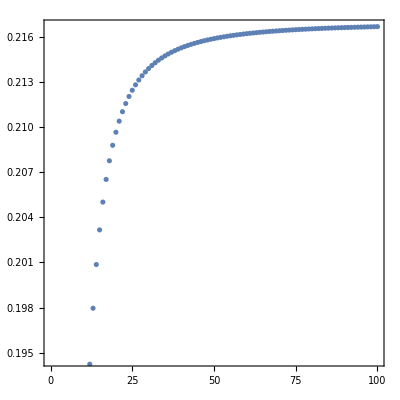

```mathematica
ListPlot[getTheoreticalSD/@Range[1, 1000,10]]
```

```mathematica
getTheoreticalBox[31]/getTheoreticalSD[1000000000]
```

0.11781

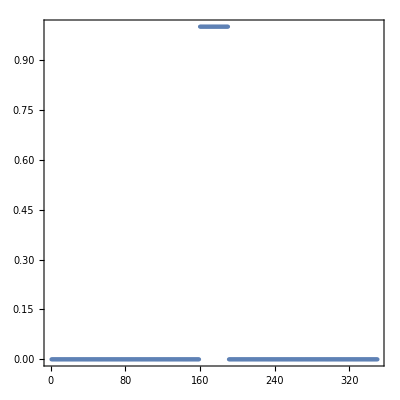

```mathematica
ListPlot[Table[{y, If[y<350/2-30/2  ||y>350/2+30/2 ||y<350/4 ,0, 1]}, {y, 1, 350.}]]
```

```mathematica
31^2*5/(150*350.)
```

0.0915238

```mathematica
1.7*5
```

8.5

## play space